```mathematica
Finite Potential Well
```

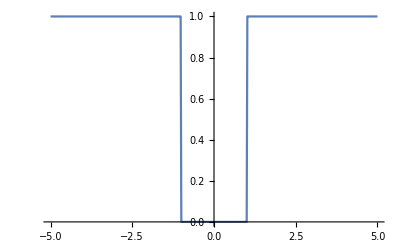

```mathematica
μ=1.0;
min=-5;max=5;step=500;
d=(max-min)/step;
V=Table[If[Abs[x]≤1,0,1],{x,Range[min,max,d]}];
ListLinePlot[V,PlotRange->All,DataRange->{min,max}]
```

```mathematica
f[En_]:=2(V-En);
```

```mathematica
u=ConstantArray[0,step];
g=ConstantArray[0,step];
u[[1]]=0;(*boundary conditions*)
g[[1]]=u[[1]](1-(d^2 f[Eni][[1]])/12);
u[[2]]=1;(*boundary conditions*)
g[[2]]=u[[2]](1-(d^2 f[Eni][[2]])/12);
(*g[[step]]=u[[step]](1-(d^2 f[[step]])/12);*)
u1=u;g1=g;
```

```mathematica
uend=0;
δ:=u[[step]]-uend;
δ1:=u1[[step]]-uend;
```

```mathematica
tail[En_]:=Do[g[[i+1]]=2 g[[i]]-g[[i-1]]+d^2 f[En][[i]]u[[i]];u[[i+1]]=g[[i+1]]/(1-(d^2 f[En][[i+1]])/12),{i,2,step-1,1}];
tail1[En_]:=Do[g1[[i+1]]=2 g1[[i]]-g1[[i-1]]+d^2 f[En][[i]]u1[[i]];u1[[i+1]]=g1[[i+1]]/(1-(d^2 f[En][[i+1]])/12),{i,2,step-1,1}];
```

```mathematica
For[En=0.1,δ δ1≥0,En+=0.0001,tail[En];tail1[En+0.0001]];
```

```mathematica
tail[0.3920]
```

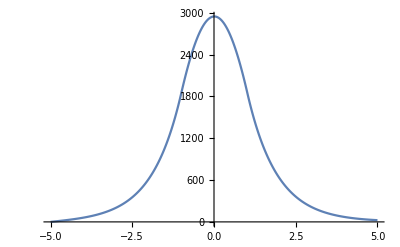

```mathematica
ListLinePlot[g,PlotRange->All,DataRange->{min,max}]
```

```mathematica
δ
```

24.6959

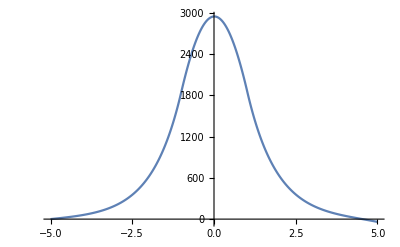

```mathematica
tail1[0.3921]
ListLinePlot[g,PlotRange->All,DataRange->{min,max}]
```

```mathematica
δ1
```

-40.4615

```mathematica
u[[step]]=u1[[step]]=0;
```

```mathematica
For[En=0.4,δ δ1≥0,En+=0.001,tail[En];tail1[En+0.001]];
```

Part::partw: Part 2 of 2[0.4] does not exist.

Part::partw: Part 3 of 2[0.4] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted